```mathematica
Needs["PlotLegends`"]
```

```mathematica
v="15";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l30k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l30k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l30k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l100k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l100k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l100k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
```

```mathematica
ngap="13";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v15=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v15=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v15=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v15=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v15=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v15=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v15=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v15=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v15=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v15=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v15=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v15=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap40v15=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
vel40v15=Table[{v40k1[[All,1]][[j]],Sum[v40k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v40k1]}];
avel40v15=Table[{av40k1[[All,1]][[j]],av40k1[[All,2]][[j]]},{j,1,Length[av40k1]}];
gap50v15=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v15=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v15=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
gap100v15=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g100k1]}];
vel100v15=Table[{v100k1[[All,1]][[j]],Sum[v100k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v100k1]}];
avel100v15=Table[{av100k1[[All,1]][[j]],av100k1[[All,2]][[j]]},{j,1,Length[av100k1]}];
```

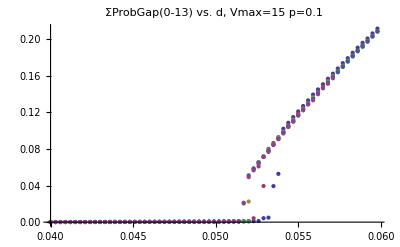

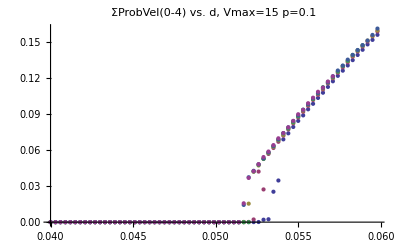

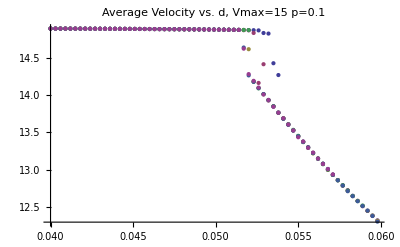

```mathematica
ListPlot[{gap10v15,gap20v15,gap30v15,gap40v15,gap50v15,gap100v15},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel10v15,vel20v15,vel30v15,vel40v15,vel50v15,vel100v15},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel10v15,avel20v15,avel30v15,avel40v15,avel50v15,avel100v15},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
ga20k1=gap20v15[[All,1]];
ga50k1=gap50v15[[All,1]];
ga20k2=gap20v15[[All,2]];
ga50k2=gap50v15[[All,2]];
```

0.235089  = val

0.0454  = d0

0.1  = α

0.1  = z

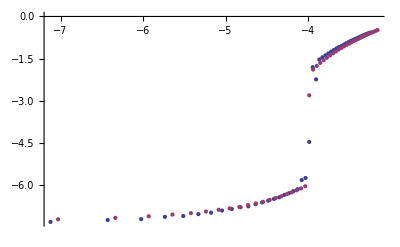

```mathematica
ga10k1=gap20v15[[All,1]];
ga50k1=gap50v15[[All,1]];
ga10k2=gap20v15[[All,2]];
ga50k2=gap50v15[[All,2]];
n1=20;
n2=50;
val=1000;
For[d0=0.045,d0<=0.05,d0+=0.0001,
For[α=0.01,α≤0.8,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[n1*1000.],
Log[ga10k2[[i]]]+α*Log[n1*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[n2*1000.],Log[ga50k2[[i]]]+α*Log[n2*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[n1*1000.],Log[ga50k1[[k]]-d0]+z*Log[n2*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[n1*1000.],Log[ga50k1[[Length[ga50k1]-1]]-d0]+z*Log[n2*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]


" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[n1*1000.],
Log[ga10k2[[i]]]+αf*Log[n1*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[n2*1000.],Log[ga50k2[[i]]]+αf*Log[n2*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

0.0454  = d0

0.1  = α

0.1  = z

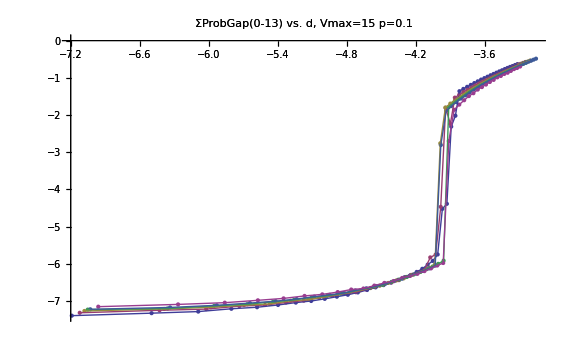

```mathematica
d0f=0.0454;
αf=0.1;
zf=0.1;
ga5k1=gap5v15[[All,1]];
ga10k1=gap10v15[[All,1]];
ga20k1=gap20v15[[All,1]];
ga30k1=gap30v15[[All,1]];
ga40k1=gap40v15[[All,1]];
ga50k1=gap50v15[[All,1]];
ga100k1=gap100v15[[All,1]];
ga5k2=gap5v15[[All,2]];
ga10k2=gap10v15[[All,2]];
ga20k2=gap20v15[[All,2]];
ga30k2=gap30v15[[All,2]];
ga40k2=gap40v15[[All,2]];
ga50k2=gap50v15[[All,2]];
ga100k2=gap100v15[[All,2]];
g5k=Table[{Log[ga5k1[[i]]-d0f]+zf*Log[5*1000.],
Log[ga5k2[[i]]]+αf*Log[5*1000.]},{i,1,Length[ga5k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g20k=Table[{Log[ga20k1[[i]]-d0f]+zf*Log[20*1000.],
Log[ga20k2[[i]]]+αf*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0f]+zf*Log[30*1000.],
Log[ga30k2[[i]]]+αf*Log[30*1000.]},{i,1,Length[ga30k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0f]+zf*Log[40*1000.],
Log[ga40k2[[i]]]+αf*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[50*1000.],Log[ga50k2[[i]]]+αf*Log[50*1000.]},{i,1,Length[ga50k1]}];
g100k=Table[{Log[ga100k1[[i]]-d0f]+zf*Log[100*1000.],
Log[ga100k2[[i]]]+αf*Log[100*1000.]},{i,1,Length[ga100k1]}];
pic1=ListPlot[{g10k,g20k,g30k,g40k,g50k,g100k},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None];
pic2=ListLinePlot[{g10k,g20k,g30k,g40k,g50k,g100k},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None];
" = d0" d0f
" = α" αf
" = z" zf
Show[{pic1,pic2}]
```